# 25: Eigenvalue Algorithms:

We know that we can not use the Characteristic Polynomial to compute eigenvalues. The question is how do we compute all the eigenvalues or more generally the eigen decomposition of a matrix A.

## Localization Pic Code

```mathematica
GershgorignPic[A_]:=Module[{m=Length[A],c,r},
Graphics[{
Table[
c=ReIm[A⟦i,i⟧];
r1=Sum[Abs[A⟦i,j⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
r2=Sum[Abs[A⟦j,i⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
{Hue[i/m],Opacity[0.2],EdgeForm[Hue[i/m]],
Disk[c,Min[r1,r2],{0,π/2}],
Disk[c,Min[r1,r2],{π/2,π}],
Disk[c,Min[r1,r2],{π,3π/2}],
Disk[c,Min[r1,r2],{3π/2,2π}]},
{i,m}],
Point[ReIm[Eigenvalues[A]]]},
Frame->True,
GridLines->Automatic]
]
```

## Companion Polynomials

Matlab computes polynomial roots by building a matrix which has the same roots.  There are actually a whole bunch of these companion matrices for a given polynomial. The most common is implemented below

```mathematica
CompanionMatrix[a_]:= Module[{m=Length[a],A},
A=SparseArray[{Band[{2,1}]->1},{m-1,m-1}];
A⟦All,m-1⟧=-a⟦1;;-2⟧/a⟦-1⟧;
A
]
```

```mathematica
p[x_]:=2 x^2+3x +1 + x^7
a=CoefficientList[p[x], x];
A=CompanionMatrix[a];
MatrixForm[A];
Sort[Eigenvalues[N[A]]]
Sort[x/.NSolve[p[x]==0,x]]
```

{-0.794993-0.359485 ⅈ,-0.794993+0.359485 ⅈ,-0.493017+0. ⅈ,-0.106686-1.20568 ⅈ,-0.106686+1.20568 ⅈ,1.14819-0.707374 ⅈ,1.14819+0.707374 ⅈ}

{-0.794993-0.359485 ⅈ,-0.794993+0.359485 ⅈ,-0.493017,-0.106686-1.20568 ⅈ,-0.106686+1.20568 ⅈ,1.14819-0.707374 ⅈ,1.14819+0.707374 ⅈ}

## Theorem 25.1: Galois

We all know the quadratic formula for the roots of a λ^2+b λ+c =0. There is a formula for the three roots of a cubic.  Here is one version!

```mathematica
Clear[a,b,c,λ]
λ/.Solve[λ^3+a λ^2+b λ+c==0,λ]
```

There is a much longer formula for the four roots of a quartic

```mathematica
Clear[a,b,c,d,λ]
λ/.Solve[λ^4+a λ^3+b λ^2+c λ +d==0,λ]
```

Abel proved in 1824 that no such general formula can exist for higher degree polynomials!  See Theorem 25.1 for a careful statement of the theorem. What this means is that algorithms to compute eigenvalues need to be iterative like Newton’s method!

## Power Method: A Simple Iterative Scheme

There is a simple way to compute the eigenvector associated with the largest eigenvalue of almost any matrix A. In words, multiply by A and normalize repeatedly.  This is very easy to code.

```mathematica
PowerMethod[A_][x_]:=Module[{z=A.x},z/Norm[z]]
```

It works!  Here is a simple test on an SPD matrix.

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
x0=RandomReal[{-1,1},m];
TableForm[PowerMethodData=NestList[PowerMethod[A], x0,34],TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | -0.873225 | -0.406332 | 0.16695 | -0.933622 | 0.773505 | 0.648259
2 | -0.131065 | 0.024428 | 0.573991 | -0.668112 | 0.454083 | -0.0139351
3 | -0.150558 | 0.0962248 | 0.579449 | -0.668642 | 0.412936 | -0.121305
4 | -0.213073 | 0.136111 | 0.563459 | -0.65226 | 0.395661 | -0.191306
5 | -0.271651 | 0.164654 | 0.544045 | -0.628921 | 0.378807 | -0.253125
6 | -0.321494 | 0.186457 | 0.523094 | -0.602937 | 0.361709 | -0.306402
7 | -0.362381 | 0.203349 | 0.502238 | -0.577034 | 0.345222 | -0.350628
8 | -0.395203 | 0.216437 | 0.482717 | -0.552888 | 0.330068 | -0.386424
9 | -0.421214 | 0.226556 | 0.465238 | -0.53136 | 0.31665 | -0.414963
10 | -0.44169 | 0.234372 | 0.450066 | -0.512742 | 0.305088 | -0.437535
11 | -0.457767 | 0.240416 | 0.437182 | -0.496978 | 0.29532 | -0.455324
12 | -0.470389 | 0.245101 | 0.426409 | -0.483825 | 0.287182 | -0.469334
13 | -0.48031 | 0.248745 | 0.417498 | -0.472967 | 0.280471 | -0.480377
14 | -0.488125 | 0.25159 | 0.410187 | -0.464069 | 0.274976 | -0.489093
15 | -0.494294 | 0.253819 | 0.404221 | -0.456817 | 0.270501 | -0.495986
16 | -0.499175 | 0.255571 | 0.399375 | -0.45093 | 0.266869 | -0.501448
17 | -0.503045 | 0.256954 | 0.39545 | -0.446166 | 0.263931 | -0.505783
18 | -0.506118 | 0.258047 | 0.392278 | -0.442318 | 0.261559 | -0.50923
19 | -0.508563 | 0.258914 | 0.38972 | -0.439216 | 0.259647 | -0.511975
20 | -0.510511 | 0.259602 | 0.38766 | -0.436718 | 0.258108 | -0.514162
21 | -0.512064 | 0.26015 | 0.386002 | -0.434709 | 0.25687 | -0.515908
22 | -0.513303 | 0.260587 | 0.38467 | -0.433094 | 0.255875 | -0.517301
23 | -0.514294 | 0.260935 | 0.383599 | -0.431797 | 0.255076 | -0.518415
24 | -0.515086 | 0.261213 | 0.382739 | -0.430755 | 0.254434 | -0.519306
25 | -0.515719 | 0.261435 | 0.382049 | -0.429919 | 0.253919 | -0.520019
26 | -0.516225 | 0.261613 | 0.381495 | -0.429248 | 0.253506 | -0.520589
27 | -0.516631 | 0.261755 | 0.38105 | -0.42871 | 0.253175 | -0.521045
28 | -0.516955 | 0.261868 | 0.380694 | -0.428278 | 0.252909 | -0.521411
29 | -0.517215 | 0.261959 | 0.380408 | -0.427932 | 0.252696 | -0.521703
30 | -0.517424 | 0.262032 | 0.380179 | -0.427655 | 0.252525 | -0.521938
31 | -0.51759 | 0.262091 | 0.379995 | -0.427432 | 0.252388 | -0.522125
32 | -0.517724 | 0.262137 | 0.379848 | -0.427254 | 0.252278 | -0.522276
33 | -0.517831 | 0.262175 | 0.37973 | -0.427111 | 0.25219 | -0.522396
34 | -0.517917 | 0.262205 | 0.379635 | -0.426996 | 0.252119 | -0.522493
35 | -0.517986 | 0.262229 | 0.379559 | -0.426904 | 0.252062 | -0.52257

It has almost converged to the eigenvector associated with the largest eigenvalue!

```mathematica
Eigensystem[A,1]
```

{{3.55898},{{0.518263,-0.262326,-0.379252,0.426533,-0.251834,0.522883}}}

This is the first iterative scheme we have seen in the course. We will come back to iterative schemes later. They have advantages:

Black-box algorithms only use the matrix rather than work on the matrix.  This is essential to exploit sparsity!

You do not have to wait for full convergence if a “rough” answer will do.

For now we are going to look at classical dense matrix eigenvalue algorithms which start with a reduction very similar to a QR decomposition and then perform an iterative step that reveals all the eigenvalues of a dense matrix.

## Preliminary Hessenberg Reduction

We are going to look and see what the first step does before we learn how to do it!

### Symmetric Matrix⟶Tri-Diagonal⟶^(k→∞)Diagonal

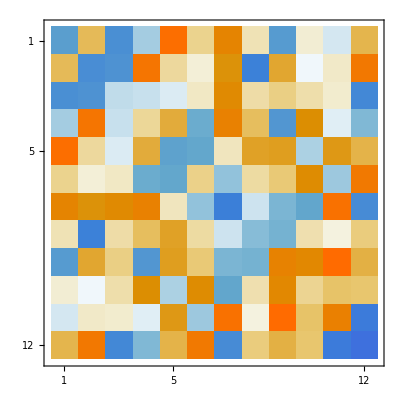
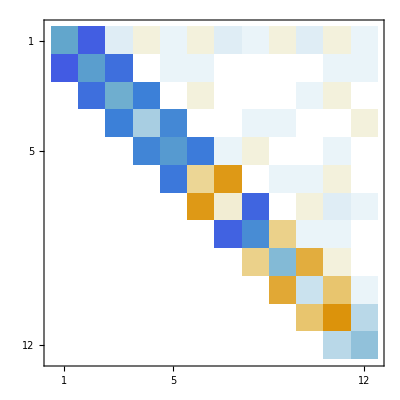
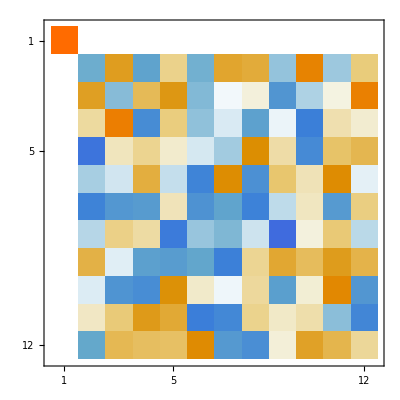

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
{Q,T}=HessenbergDecomposition[A];
Map[MatrixPlot,{A,T,Q}]
```

```mathematica
TabView[{"A"->GershgorignPic[A],"T"->GershgorignPic[T]}]
```

12

The tridiagonal matrix give tighter bounds. If we could make it more diagonal we would be able to isolate the eigenvalues.  This is the plan.  For symmetric matrices we are going to work out how to make the tridiagonal matrix more diagonal.

### General Matrix⟶Almost Upper Triangular⟶^(k→∞)UT

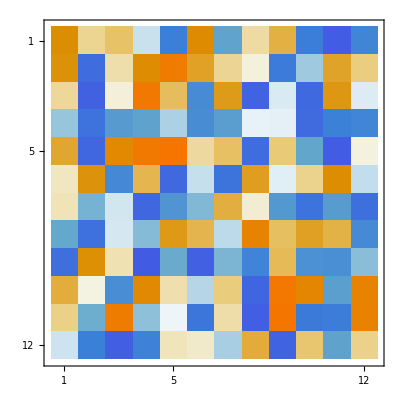
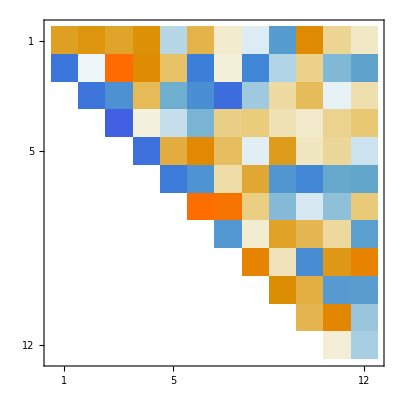
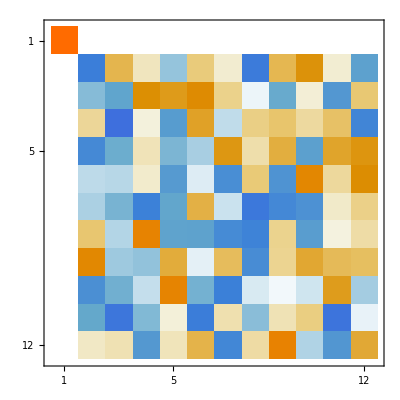

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; 
{Q,H}=HessenbergDecomposition[A];
Map[MatrixPlot,{A,H,Q}]
```

```mathematica
TabView[{"A"->GershgorignPic[A],"H"->GershgorignPic[H]}]
```

12

The almost upper triangular matrix give tighter bounds. If we could make it more upper triangular we would be able to isolate the eigenvalues.  This is the plan.  For general matrices we are going to work out how to make the almost upper triangular matrix more upper triangular.